```mathematica
m=5
```

5

```mathematica
BitRotateLeft[x_,n_]:=BitAnd[BitXor[BitShiftLeft[x,n],BitShiftRight[x,m-n]],2^m-1]

BitRotateLeft[x_]:=BitAnd[BitXor[BitShiftLeft[x],BitShiftRight[x,m-1]],2^(m+1)-1]
CHI[x_]:=BitAnd[BitXor[x,BitNot[xxb=BitRotateLeft[x]],BitRotateLeft[xxb]],2^m-1]
Table[CHI[i],{i,0,2^m}]
Union@Table[CHI[i],{i,0,2^m}]
```

{31,24,17,22,3,4,13,10,6,1,8,15,26,29,20,19,14,9,0,7,18,21,28,27,23,16,25,30,11,12,5,2,25}

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
S[x_]:=CHI[x]
```

```mathematica
4
```

4

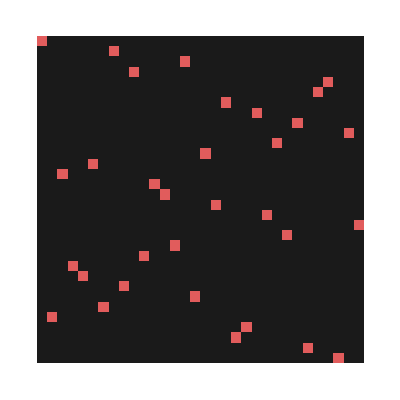

```mathematica
DDT[delta_]:=(
Delta=Table[BitXor[S[BitXor[x,delta]],S[x]],{x,0,2^m-1}];
Map[{delta,#}+1->Count[Delta,#]&,Union[Delta]])

DDT[]:=Flatten[Table[DDT[delta],{delta,0,2^m-1}],1]

ArrayPlot[SparseArray[DDT[]],ColorFunction->"WatermelonColors"]
```

```mathematica
SparseArray[DDT[]]//MatrixForm
```

(32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0)

```mathematica
jyu
```

```mathematica
DDT[10]
```

{{11,24}→32}

```mathematica
CHI[x_]:=BitAnd[BitXor[x,BitAnd[BitNot[xxb=BitRotateLeft[x]],BitRotateLeft[xxb],2^m-1]],2^(m)-1]
```

```mathematica
Union@Table[CHI[i],{i,0,2^m}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
x=11
IntegerDigits[x,2,m]
xx=BitRotateLeft[x]
IntegerDigits[xx,2,m]
IntegerDigits[BitAnd[BitNot[xx],2^5-1],2,m]
BitAnd[BitXor[BitNot[xx],2^m-1,yy= BitRotateLeft[xx]],x]
IntegerDigits[yy,2,5]
```

11

{0,1,0,1,1}

22

{1,0,1,1,0}

{0,1,0,0,1}

11

{0,1,1,0,1}

```mathematica
SymCHI[x_]:=x+(RotateLeft[x,1]+1)RotateLeft[x,2]
```

```mathematica
SymCHI[{x0,x1,x2,x3,x4}]
```

{x0+(1+x1) x2,x1+(1+x2) x3,x2+(1+x3) x4,x3+x0 (1+x4),(1+x0) x1+x4}

```mathematica
RotateLeft[xx]
Mod[((xx=RotateLeft[(x=IntegerDigits[11,2,m])])+1),2]
Mod[((xx=RotateLeft[(x=IntegerDigits[11,2,m])])+1)*RotateLeft[xx],2]
```

{0,1,1,0,1}

{0,1,0,0,1}

{0,1,0,0,1}

```mathematica
xx
```

{1,0,1,1,0}

```mathematica
BitAnd[BitXor[11,BitAnd[BitNot[xxb=BitRotateLeft[11]],BitRotateLeft[xxb],2^m-1]],2^(m)-1]
```

2

```mathematica
Mod[SymCHI[IntegerDigits[11,2,5]],2]
```

{0,0,0,1,0}

```mathematica
d={d0,d1,d2,d3,d4}
x={x0,x1,x2,x3,x4}
Delta=PolynomialMod[SymCHI[x+d]+SymCHI[x],2];Delta//TableForm
```

{d0,d1,d2,d3,d4}

{x0,x1,x2,x3,x4}

d0+d2+d1 d2+d2 x1+d1 x2
d1+d3+d2 d3+d3 x2+d2 x3
d2+d4+d3 d4+d4 x3+d3 x4
d0+d3+d0 d4+d4 x0+d0 x4
d1+d0 d1+d4+d1 x0+d0 x1

```mathematica
delta=IntegerDigits[12,2,m]
sD=PolynomialMod[Delta/.Thread[d->delta],2]
ddt=Table[
PolynomialMod[sD/.Thread[x->IntegerDigits[k,2,m]],2],{k,0,2^m-1}];
Sort[ddt]//TableForm
Tally[ddt]
```

{0,1,1,0,0}

{x1+x2,1+x3,1,0,1+x0}

0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 0 | 1

{{{0,1,1,0,1},4},{{0,0,1,0,1},4},{{1,1,1,0,1},4},{{1,0,1,0,1},4},{{0,1,1,0,0},4},{{0,0,1,0,0},4},{{1,1,1,0,0},4},{{1,0,1,0,0},4}}

```mathematica
DDT[12]
```

{{13,6}→32}